```mathematica
c=
```

```mathematica
pic = Import["/Users/jan-hendrikprinz/Desktop/IMG_1597.jpeg"]
```

-Graphics-

```mathematica
EdgeDetect[pic,10]
```

-Graphics-

```mathematica
pic
```

```mathematica
picData=ImageData[ColorConvert[pic,"GrayScale"]];
```

```mathematica
picData//Dimensions
```

{716,1428}

```mathematica
Binarize[i,{.30,.5}]
```

-Graphics-

```mathematica
i=pic;
cells=SelectComponents[Binarize[i,{.35,.5}],{"Circularity","Holes"},0.3<#1<1000&&#2≥1&]
```

-Graphics-

```mathematica
539
```

```mathematica
po=circles[[{1,2,11},1]]
```

{{538.86,636.053},{888.187,635.161},{539.451,400.847}}

```mathematica
xDir=(po[[2]]-po[[1]])/3;
yDir=(po[[3]]-po[[1]])/2.01;
pp[x_,y_]:=xDir*(x-5)+yDir*(y-1)+po[[1]]
```

```mathematica
Dimensions@picData
```

{716,1428}

```mathematica
MatrixPlot[1-picData,ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
MatrixPlot[1-picData2,ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
picData2=picData;
meanBrightness=Table[Median@Flatten@Table[
place=Dimensions[picData]-Reverse@Round@pp[x,y]+{sx,sy};
picData2[[place[[1]],place[[2]]]]=0;
Extract[picData,Dimensions[picData]-Reverse@Round@pp[x,y]+{sx,sy}],{sx,-10,10},{sy,-10,10}]
,{x,12},{y,6}];
```

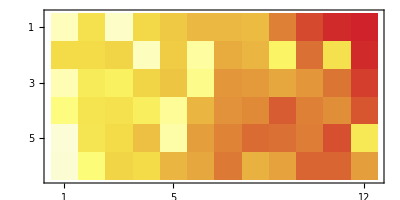

```mathematica
MatrixPlot[1-Transpose@Reverse@meanBrightness,ColorFunction->"TemperatureMap"]
```

```mathematica
Binarize
```

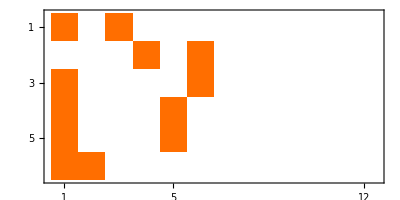

```mathematica
Map[If[#>0.6,1,0]&,Transpose@Reverse@meanBrightness,{2}]//MatrixPlot
```

```mathematica
circles=ComponentMeasurements[ImageMultiply[i,cells],{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[i,Graphics[{Red,Thick,Table[Circle[pp[x,y],10],{x,12},{y,8}]}],ImageSize->600]
```

-Graphics-

```mathematica
circles=ComponentMeasurements[ImageMultiply[i,cells],{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[i,Graphics[{Red,Thick,Circle@@#&/@circles[[{1,2,11}]]}],ImageSize->200]
```

-Graphics-

```mathematica
MatrixPlot[picData,Epilog->{Table[Point[{x,y}],{x,1,2},{y,1,2}]}]
```

-Graphics-

```mathematica
MorphologicalBinarize
```

```mathematica
ImageCorrespondingPoints
```

```mathematica
data=ImportString["0   14053  2154  2174  2055  3582  1731  4800  5094
1   13733  4257  2890  2287  2292  2068  5166  5091
2    4900  3697  2694  1867  2001  1788  5651  6026
3    8110  3143  2338  1925  1903  1856  6044  5245
4    3946  3148  2137  1740  1934  2057  5458  5265
5    3020  2230  2280  1978  1835  2359  5264  5127
6    2347  2024  1932  1803  1738  1984  5472  5429
7    2176  2060  1812  1790  1878  1742  5490  5213
8    2299  2100  2124  1558  1955  1910  4999  5143
9    2136  2147  2042  2069  1622  1850  4954  5331
10   2101  1806  1883  1637  1686  1805  5718  5284
11   1827  1903  1956  1937  1756  1883  5805  5440
","Table"];
data=Transpose[data[[All,Range[2,7]]]];
```

```mathematica
bin={{},
}
```

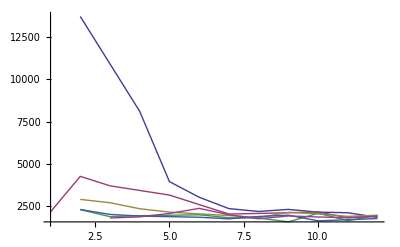

```mathematica
ListPlot[Map[Select[Transpose[{Range[12],#}],(#[[2]]>0&)]&,mask*data],Joined->True,PlotRange->All]
```

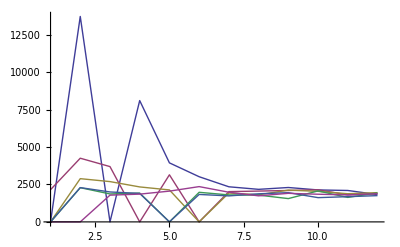

```mathematica
ListPlot[data*mask,Joined->True,PlotRange->All]
```

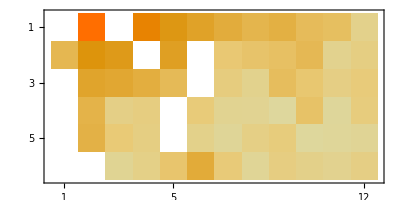

```mathematica
MatrixPlot[data*mask]
```

```mathematica
mask//Dimensions
```

{4}